```mathematica
(*Final*)
```

```mathematica
(* ---------------- vars ----------------*)
nVars=0;
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
qs={};
qsvars={};
qsInit={};
dqsInit={};
(* ------------ objects ----------------- *)
nObjects=0;
objNames={};
(* Properties *)
masses={};
inertias={};
lens={};
g=9.8;
(* Transformation matrices *)
Ts={};
pFronts={};
pBacks={};

(* Vertices for impact detection *)
impObjVertexs={};
impObjVertexGroupIDs={};
(* Edges for impact detection *)
impObjEdges={};
impObjEdgeGroupIDs={};

(* ------------ Create objects ----------------- *)

CreateOneLink[linkgeometry_,options_]:=Module[{l,T,pFront,pBack},
nObjects=nObjects+1;
If[options=="BaseLink",(
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];

(*Vars*)
nDOF=3;
{objqs,objqsvars}=pushVars[nDOF];
x=objqs[[1]];
y=objqs[[2]];
θ=objqs[[3]];
{T,pFront,pBack}=CalcAndPushT[x,y,θ,l];

objqsinit={(p1x+p2x)/2,(p1y+p2y)/2,myArcTan[p1x,p1y,p2x,p2y]};
qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,Table[RandomReal[]*0.5,{i,1,nDOF}]];

(*Impact*)
PushVertex[pFront,nthGroup];
PushVertex[pBack,nthGroup];

PushEdge[{pFront[[1;;2,1]],pBack[[1;;2,1]]},nthGroup];
)];
If[options=="AppendLink",(

{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];

(*Vars*)
nDOF=1;
{objqs,objqsvars}=pushVars[nDOF];
x=(p1x+p2x)/2;
y=(p1y+p2y)/2;
θ=objqs[[1]];
{T,pFront,pBack}=CalcAndPushT[x,y,θ,l];

objqsinit={myArcTan[p1x,p1y,p2x,p2y]};
qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,Table[RandomReal[]*0.5,{i,1,nDOF}]];

(*Impact*)
PushVertex[pFront,nthGroup];
PushEdge[{pFront[[1;;2,1]],pBack[[1;;2,1]]},nthGroup];

)];
If[options=="Wall",(
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];
x=(p1x+p2x)/2;
y=(p1y+p2y)/2;
θ=myArcTan[p1x,p1y,p2x,p2y];
{T,pFront,pBack}=CalcAndPushT[x,y,θ,l];

PushVertex[pFront,nthGroup];
PushVertex[pBack,nthGroup];
PushEdge[linkgeometry,nthGroup];
)];

(* --------------------------------------- *)
(* mass and inertia*)
mass=lToMass[l];
inertia=lToInertia[l];
AppendTo[masses,mass];
AppendTo[inertias,inertia];
AppendTo[lens,l];
(*Return*)
{T,pFront,pBack}
]

nthGroup=1;
{T1,pFront1,pBack1}=CreateOneLink[{{-0.5,-0.5},{0.5,0.5}},"BaseLink"];

nthGroup=10;
pps={{-2,+2},{+2,+2},{+2,-0.7},{-2,-0.7},{-2,+2}};
For[i=1,i≤4,i++,CreateOneLink[{pps[[i]],pps[[i+1]]},"Wall"]];
```

```mathematica
cons=Simplify[{
(*pFront1[[1,1]]-pBack2[[1,1]],
pFront1[[2,1]]-pBack2[[2,1]]
pFront1[[2,1]],pFront1[[1,1]],pBack2[[1,1]],pBack2[[2,1]]*)
},qs∈Reals];
```

```mathematica
(* Remove duplicated vertices *)
n=Length[impObjVertexs];
tmpimpObjVertexs={};
tmpimpObjVertexGroupIDs={};
For[i=1,i≤n,i=i+1,
ifDup=False;
x0=impObjVertexs[[i,1,1]];
y0=impObjVertexs[[i,2,1]];
For[j=1,j≤Length[tmpimpObjVertexs],j=j+1,
If[tmpimpObjVertexs[[j,1,1]]==x0 &&tmpimpObjVertexs[[j,2,1]]==y0,
ifDup=True;
Break[]
]];
If[ifDup==False,
AppendTo[tmpimpObjVertexs,impObjVertexs[[i]]];
AppendTo[tmpimpObjVertexGroupIDs,impObjVertexGroupIDs[[i]]]
];
];
impObjVertexs=tmpimpObjVertexs;
impObjVertexGroupIDs=tmpimpObjVertexGroupIDs;
```

```mathematica
(* Prepare *)
dqs=D[qs,t];
ddqs=D[dqs,t];
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Simplify[Total[Join[KEs,-PEs]],qs∈Reals];
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=Simplify[D[D[Lag,{dqs}],t]-D[Lag,{qs}],qs∈Reals];
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*
conslink1P1x=p1Ends[[1]][[2,1]];(* y=0 *)
conslink1P1y=p1Ends[[2]][[2,1]];(* y=0 *)
*)
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=Simplify[D[D[cons,t],t],qs∈Reals])];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=TurnToEq[consddt,ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=Simplify[TurnToEq[ELeqsLeft,externalForces],qs∈Reals];
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* ----------------------------- *)
(* Preprae for NDSolve *)
timeend=2;
MAXIMPACTTIMES=200;
impactDetectionError=0.1;
intergrationMaxStepSize=0.01;
ifprint=True;

SetUpImpacts[]
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

(* NDsolve *)
{end,data,bounces}=BouncingBall[qsInit,dqsInit];
```

Impact at: t=0.128331,impactcase=7

disCurr={1.54354,1.52463,1.15646,2.47537,2.6,2.46478,0.1,1.53522,-0.112818,2.87531,-1.90775,1.08038},disPrev=0.1

Before reflection, q={0.00529726,-0.0717688,0.843586},dq={0.041278,-1.18807,0.453417}

After reflection{0.041278,1.23564,-0.352211}

Impact at: t=0.416158,impactcase=7

disCurr={1.64411,1.4617,1.05589,2.5383,2.6,2.50394,0.1,1.49606,0.223678,2.92735,-1.76616,0.937515},disPrev=0.1

Before reflection, q={0.0171782,-0.122054,0.74221},dq={0.041278,-1.58505,-0.352211}

After reflection{0.041278,0.766419,-1.2187}

Impact at: t=0.72105,impactcase=7

disCurr={2.08776,1.31114,0.612242,2.68886,2.6,2.62933,0.1,1.37067,1.47108,2.91992,-1.04558,0.403261},disPrev=0.1

Before reflection, q={0.0297635,-0.343879,0.370638},dq={0.041278,-2.22153,-1.2187}

After reflection{0.041278,-0.0515077,-2.23003}

Impact at: t=0.920093,impactcase=3

disCurr={2.6,1.25681,0.1,2.74319,2.49652,2.66723,0.203479,1.33277,2.68499,2.39231,-0.00777071,-0.300452},disPrev=0.203479

Before reflection, q={0.0379796,-0.548261,-0.0732359},dq={0.041278,-2.00213,-2.23003}

After reflection{0.041278,3.28733,0.407607}

Impact at: t=1.56516,impactcase=7

disCurr={2.33333,1.24097,0.366669,2.75903,2.6,2.62982,0.1,1.37018,2.05747,2.81173,-0.594093,0.16016},disPrev=0.1

Before reflection, q={0.0646067,-0.466666,0.189699},dq={0.041278,-3.03435,0.407607}

After reflection{0.041278,1.91337,-2.02187}

Impact at: t=1.85647,impactcase=3

disCurr={2.6,1.27188,0.1,2.72812,2.05021,2.57485,0.649795,1.42515,2.88994,1.33489,0.402329,-1.15273},disPrev=0.649795

Before reflection, q={0.0766314,-0.325103,-0.399289},dq={0.041278,-0.941455,-2.02187}

After reflection{0.041278,2.53311,-0.421248}

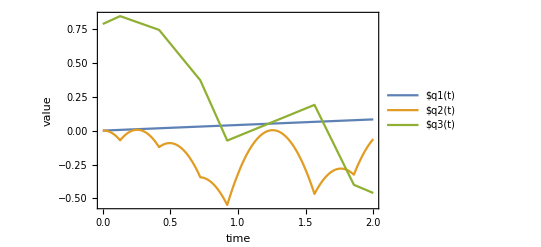

```mathematica
(* Plot *)
qsPlot=Table[Piecewise[qsvars[[i]]/.data],{i,1,nVars}];
Show[Plot[Evaluate[qsPlot],{t,0,end},PlotLegends->qs,
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]]
```

```mathematica
plotGetLinkCoords[T_,l_]:=Module[{pFront,pBack},
p0x=T[[1,4]];
p0y=T[[2,4]];
pFront=T.Transpose[{{l/2,0,0,1}}]//Simplify;
pBack=T.Transpose[{{-l/2,0,0,1}}]//Simplify;
Line[{pFront[[1;;2,1]],pBack[[1;;2,1]]}]
]
links=Table[plotGetLinkCoords[Ts[[i]],lens[[i]]],{i,1,nObjects}];
```

```mathematica
(* Animate *)
(*linksCoords[i_]:=(links[[i]]/.sim)[[1]];*)
linksCoords[j_]:=links[[j]]/.Table[qs[[i]]->qsPlot[[i]],{i,1,nVars}];
LinksForAnimation[tt_]:=(Table[linksCoords[i],{i,1,Length[links]}])/.t->tt;
Animate[Show[
{Graphics[LinksForAnimation[t]]
},PlotRange-> {{-5,5},{-5,5}},Frame-> True],{t,0,timeend}]
```